# e.All.Numeric.rencon1.fch.nb

```mathematica
NotebookFileName[]
```

C:\Users\Tom\Desktop\octet.sea-valence\e.All.Numeric.series-o0.recon1.strange.sea-valence.strong-only.fch.L-1.00.nb

```mathematica
Quit[]
```

## note

use full integral analytic expression to draw pictures.

s flavor in proton has no contribution, so  the rencon is zero.

for perspective quark, use perspective fucoeandmrrlnm

this nb is to numeric evaluating the Γμs

and draw pictures.

if consider 1/((1+Q^2/Λ^2)^2)→c^2/((1+Q^2/Λ^2)^2) ,c^2=((Λ^2+mπ^2)/Λ^2)^2,then c^2={1.05349 mπ, 1.79549 mKi, 2.0984 mη}

for different particles, use different rencon

## Initial

```mathematica
Quit[]
```

```mathematica
Clear["Global`*"]
```

inital by hand

```mathematica
<<X`
```

Package-X v2.1.1 already initialized
For more information, see the

```mathematica
choplimit=10^-8;
```

## coefficients & mass constants

a 4 component list, contain all, u,d,s

coe list and mass rule list initial

```mathematica
Once[fucoe=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

```mathematica
Once[fumass=Table[0,{k,1,13,1},{i,1,11,1},{i,1,8,1}]];
```

coe list and mass rule get

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-storage.o0/"}]]
```

C:\Users\Tom\Desktop\octet.sea-valence\expression-storage.o0

```mathematica
fucoeandmrrlnm={
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.all.m"}],
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.u.m"}],
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.d.m"}],
FileNameJoin[{Directory[],"fu.coeandmassrrl.consti.s.m"}]
};
```

```mathematica
Once[chpt`qfb`quench`coemass=Get[FileNameJoin[{Directory[],"chpt`qfb`quench`coemass.m"}]]];
Once[chpt`qfa`sea`coemass=Get[FileNameJoin[{Directory[],"chpt`qfa`sea`coemass.m"}]]];
Once[chpt`qfa`valence`coemass=Get[FileNameJoin[{Directory[],"chpt`qfa`valence`coemass.m"}]]];
```

```mathematica
Once[
fucoeandmrrlraw=Map[Get,fucoeandmrrlnm,1]
];
```

```mathematica
fucoeandmrrlraw//Dimensions
```

{4,11,8}

```mathematica
Once[
fucoeandmrrl=Join[fucoeandmrrlraw,
Transpose[chpt`qfb`quench`coemass,{2,3,1}],
Transpose[chpt`qfa`valence`coemass,{2,3,1}],
Transpose[chpt`qfa`sea`coemass,{2,3,1}]
]
];
```

```mathematica
fucoeandmrrl//Dimensions
```

{13,11,8}

mass constant

## order

conmo={1Σ,2Neu,3Ξ,4Λ}--{1Σm,2Σ0,3Σp,4pr,5ne,6Ξm,7Ξ0,8Λ}

conmm={1π,2Ki,3η},

conmd={1Δ,2Σs,3Ξs,4Ω}

## assign value

```mathematica
Once[
{conmπ,conmKi,conmη,conmEtas}={
0.1381,
0.1381,
0.1381,
0.1381
}
];
```

```mathematica
Once[
{conmΣ,conmN,conmΞ,conmΛ,conmΛΣ,
conmUUU,conmDDD,conmSSS(* the symmetric terms *)
}={
0.939,0.939,0.939,0.939,0.939,
0.939,0.939,0.939
}
];
```

```mathematica
{conmΔ,conmΣs,conmΞs,conmΩ}={
1.232,
1.232,
1.232,
1.232
};
```

```mathematica
{conmN,conmη,conmΞs}
```

{0.939,0.5693,1.53}

fu Coefficients mass rules reduce

## fu Coefficients

in {4,9} external sign[-]

fusign8,fusign9

```mathematica
fucoepresign={
(*+++++++++++++++++++111++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,fusign8,(*8*)fusign9,(*9*)
1,1(*11*)},
(*+++++++++++++++++++222++++++++++++++++++++++++++++++++++++++*)
{1,1,1,
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)},
(*+++++++++++++++++++333++++++++++++++++++++++++++++++++++++++*)
{1,1,1,(*3*)
-1,(*4*)-1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)}(*fch's sign*)
}⟦3⟧;
```

1 for fitting, 2 for calc/test,

```mathematica
(*fucoeandmrrlraw [consti,figure,octet][4*11*8]*)
fucoe=Table[
Simplify[
fucoepresign*Values[fucoeandmrrl⟦i⟧]
]
,{i,1,13,1}
];//AbsoluteTiming
```

{1.91217,Null}

## fu mass rules

```mathematica
fumass=Keys[fucoeandmrrl];
```

```mathematica
fucoe//Dimensions
fumass//Dimensions
```

{13,11,8}

{13,11,8}

magnetic momentum tree level

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613};

rule lists

```mathematica
constmo={
(*1*)conmΣ,(*2*)conmΣ,(*3*)conmΣ,
(*4*)conmN,(*5*)conmN,
(*6*)conmΞ,(*7*)conmΞ,
(*8*)conmΛ
};
```

```mathematica
baselist1={
{mN->conmΣ},{mN->conmΣ},{mN->conmΣ},
{mN->conmN},{mN->conmN},
{mN->conmΞ},{mN->conmΞ},
{mN->conmΛ}
};
```

c1→2.081,c2→(2/3 c1-1),c3→(-1/3 c1-1)

```mathematica
c3 = c2 - c1;
```

```mathematica
baselist2={
f->0.093,
zi->-1,
di->0.76,fi->0.50,
Λ0->1,ci->1.5,
c1->1.5615941264527964,c2->0.4980732797896622
};
```

for neutron pull-apart, best octet fit Λ0≈1~0.1

```mathematica
baselist=Table[
Join[baselist1⟦i⟧,baselist2]
,{i,1,8,1}
];
```

## para test c1c2 sum-square all-baryons

Λ0→0.80,ci→1.5,
{0.124785,{c1→1.79817,c2→0.510024}}

Λ0→0.85,ci→1.5,
{0.124892,{c1→1.73678,c2→0.502641}}

Λ0→0.90,ci→1.5,
{0.126503,{c1→1.67663,c2→0.498392}}

Λ0→1,ci→1.5,
{0.13259,{c1→1.56159,c2→0.498073}}

*********************************************************************

ci→1,Λ0→0.7,
{0.18488,{c1→2.08636,c2→0.534415}}

ci→1,Λ0→0.75,
{0.182312,{c1→2.04853,c2→0.516187}}

ci→1,Λ0→0.8,
{0.182242,{c1→2.01074,c2→0.499423}}

ci→1,Λ0→0.85,
{0.184055,{c1→1.97336,c2→0.484188}}

ci→1,Λ0→0.90,
{0.187237,{c1→1.93672,c2→0.470496}}

ci→1,Λ0→0.95
{0.191372,{c1→1.90108,c2→0.4583}}

ci→1,Λ0→1.0,
{0.196131,{c1→1.86666,c2→0.4475}}

ci→1,Λ0→1.05,
{0.201258,{c1→1.83359,c2→0.437936}}

ci→1,Λ0→1.1,
{0.206563,{c1→1.80199,c2→0.429402}}

**********************************************************************************

ci→1,Λ0→0.90,
{0.187237,{c1→1.93672,c2→0.470496}}

Λ0→0.90,ci→1.05,
{0.180487,{c1→1.9108,c2→0.470493}}

Λ0→0.90,ci→1.1,
{0.17385,{c1→1.88487,c2→0.47114}}

Λ0→0.90,ci→1.15,
{0.16734,{c1→1.85892,c2→0.472429}}

Λ0→0.90,ci→1.2,

{0.160973,{c1→1.83296,c2→0.474349}}

Λ0→0.90,ci→1.25,
{0.154763,{c1→1.80698,c2→0.476887}}

Λ0→0.90,ci→1.3,
{0.148722,{c1→1.78098,c2→0.480032}}

Λ0→0.90,ci→1.35,

{0.142864,{c1→1.75495,c2→0.483769}}

Λ0→0.90,ci→1.40,
{0.137201,{c1→1.72888,c2→0.488085}}

Λ0→0.90,ci→1.45,
{0.131743,{c1→1.70278,c2→0.492964}}

Λ0→0.90,ci→1.5,
{0.126503,{c1→1.67663,c2→0.498392}}

*************************************************************************

Λ0→0.80,ci→1,
{0.182242,{c1→2.01074,c2→0.499423}}

Λ0→0.80,ci→1.05,
{0.176004,{c1→1.99001,c2→0.498533}}

Λ0→0.80,ci→1.1,
{0.169839,{c1→1.96916,c2→0.498082}}

Λ0→0.80,ci→1.15,
{0.163762,{c1→1.94819,c2→0.498068}}

Λ0→0.80,ci→1.2,

{0.157786,{c1→1.92711,c2→0.498491}}

Λ0→0.80,ci→1.25,
{0.151925,{c1→1.90591,c2→0.499347}}

Λ0→0.80,ci→1.3,
{0.146192,{c1→1.88459,c2→0.500634}}

Λ0→0.80,ci→1.35,

{0.140599,{c1→1.86316,c2→0.502349}}

Λ0→0.80,ci→1.40,
{0.13516,{c1→1.84161,c2→0.504489}}

Λ0→0.80,ci→1.45,
{0.129884,{c1→1.81995,c2→0.507049}}

Λ0→0.80,ci→1.5,
{0.124785,{c1→1.79817,c2→0.510024}}

************************************************************

Λ0→0.85,ci→1.5,
{0.124892,{c1→1.73678,c2→0.502641}}

Λ0→1,ci→1.5,
{0.13259,{c1→1.56159,c2→0.498073}}

## para test c1c2 sum - square

fch,ci→1,Λ0→0.9,
c1→2.081,c2→0.788,c3→-1.693
{0.0434328,{c1→2.00193}}

ci→1,Λ0→0.8,
 {4.55972×10^-17,{c1→2.14188,c2→0.756261}}

ci→1,Λ0→0.85,
 {6.40949×10^-31,{c1→2.09749,c2→0.752286}}

ci→1,Λ0→0.90,
 {1.33761×10^-17,{c1→2.05739,c2→0.747545}}

ci→1,Λ0→0.95
 {3.9443×10^-31,{c1→2.02149,c2→0.741624}}

ci→1,Λ0→1.0,
 {1.32802×10^-16,{c1→1.98969,c2→0.734099}}

## Γμ get

pure diagram form-factor

```mathematica
Clear[ff1,ff2]
```

```mathematica
Once[Monitor[
ff1=Table[
Get[
FileNameJoin[{Directory[],"f1."<>"analytic."<>ToString[i]<>".m"}]
]
,{i,1,11,1}];
ff2=Table[
Get[
FileNameJoin[{Directory[],"f2."<>"analytic."<>ToString[j]<>".m"}]
]
,{j,1,11,1}];
,{i,j}]//AbsoluteTiming]
```

{0.180975,Null}

form-factor f1, f2

## form-factor list

fucoe=11[diagram]*8[octet]*n(a coefficients lists of n elements)

fumass=11[diagram]*8[octet]*n(n ==above n,n mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
fucoe[[2,4]]
```

```mathematica
Length[fucoe[[2,4]]]
```

contribution combine coefficients,f1, f2

```mathematica
SetOptions[Simplify,TimeConstraint->1];
```

fucoe=11[diagram]*8[octet]*n(coefficients)

fumass=11[diagram]*8[octet]*n(n =above n,mass rule lists)

diagff=11[diagram]*2[ff1,ff2]*many(contri terms)

```mathematica
Once[nuff1=Table[0,{constituent,1,13,1}]];
Once[nuff2=Table[0,{constituent,1,13,1}]];
```

```mathematica
Monitor[
Table[
(
nuff1⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,if,io,coe⟧*ff1⟦if⟧
)/.baselist⟦io⟧
)/.fumass⟦constituent,if,io,coe⟧
]
,{io,1,8,1}(*the outest level is the octet order*)
,{if,1,11,1}(*the figures contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,if,io⟧],1}(*the coe contris should be summed*)
]
,{2,3}
]
);
(
nuff2⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,if,io,coe⟧*ff2⟦if⟧
)/.baselist⟦io⟧/.baselist⟦io⟧
)/.fumass⟦constituent,if,io,coe⟧
]
,{io,1,8,1}(*the outest level is the octet order*)
,{if,1,11,1}(*the figures contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,if,io⟧],1}(*the coe contris should be summed*)
]
,{2,3}
]
);
,{constituent,1,13,1}
];
,{constituent,io,if,coe}
]//AbsoluteTiming
```

{34.7439,Null}

```mathematica
(*nuff1,nuff2 is 4*8*)
nugegm=Transpose[(*8*4*2 transpose into 4*8*2*)
Table[
-1/(16 π^2){
nuff1⟦;;,i⟧-Q2/(4 constmo⟦i⟧^2)nuff2⟦;;,i⟧,
nuff1⟦;;,i⟧+nuff2⟦;;,i⟧
}
,{i,1,8,1}]
,{2,3,1}
];//AbsoluteTiming
```

{0.0037401,Null}

```mathematica
nuff1//Dimensions
nuff2//Dimensions
nugegm//Dimensions
```

{13,8}

{13,8}

{13,8,2}

## tree level contributions

initial

because history reasons, all mass mo here is marked as mN

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(c1 Q2)/(√3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)+(4 c1 mN^2)/(√3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

{(c1 Q2)/(3 (4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2), (4 c1 mN^2)/(3(4 mN^2+Q2))Λ^4/((Λ^2+Q2)^2)},(*2,Σ0*)

```mathematica
trf1f2={
(*+++++++++++++++++total++++++++++++++++++++++++*)
{{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c2) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((-12 mo^2+(c1-3 (1+c2)) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-3 c2) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},{-(2 c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(8 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)},
{-(c1 Q2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),-(4 c1 mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}},
(*+++++++++++++++++u++++++++++++++++++++++++*)
{
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++d++++++++++++++++++++++++*)
{
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+(1+c1+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}
},
(*+++++++++++++++++s++++++++++++++++++++++++*)
{{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((4 mo^2+Q2+c3 Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 c3 mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((c1-c2+c3) Q2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1-c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},{((8 mo^2+(2+c1+c2+c3) Q2) Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (c1+c2+c3) mo^2 Λ0^4)/((4 mo^2+Q2) (Q2+Λ0^2)^2)},
{((12 mo^2+(3+4 c1+3 c3) Q2) Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2),(4 (4 c1+3 c3) mo^2 Λ0^4)/(3 (4 mo^2+Q2) (Q2+Λ0^2)^2)}}
}/.mo->mN;
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

gegm

-I el(4 mN^2+c1 Q2)/(4 mN^2+Q2) ,--el/(2mN)(4 (c1-1) mN^2)/(4 mN^2+Q2)

netrf1f2⟦4⟧={(4 mN^2+c1 Q2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2),(4 (c1-1) mN^2)/(4 mN^2+Q2)Λ^4/((Λ^2+Q2)^2)}/.baselist

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
```

```mathematica
trgegm=Transpose[
Table[
Simplify[
{
trf1f2⟦;;,i,1⟧-Q2/(4 constmo⟦i⟧^2)trf1f2⟦;;,i,2⟧,
trf1f2⟦;;,i,1⟧+trf1f2⟦;;,i,2⟧
}/.baselist⟦i⟧
]
,{i,1,8,1}]
,{2,3,1}];//AbsoluteTiming
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

{0.0159961,Null}

```mathematica
trgegm//Dimensions
```

{4,8,2}

plot

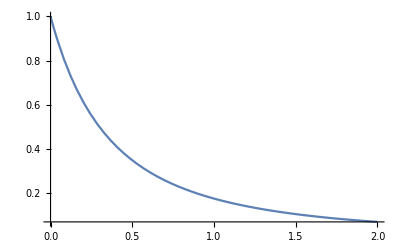

```mathematica
Plot[
trgegm⟦4,1⟧
,{Q2,0.,2.},PlotRange->Full
]
```

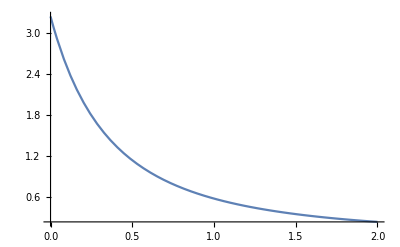

```mathematica
Plot[
trgegm⟦4,2⟧
,{Q2,0.,2.},PlotRange->Full
]
```

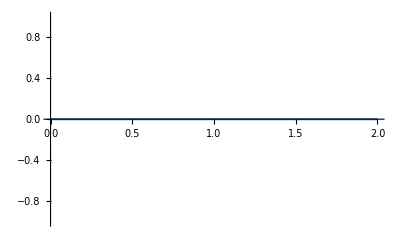

```mathematica
Plot[
trgegm⟦5,1⟧
,{Q2,0.,2.},PlotRange->Full]
```

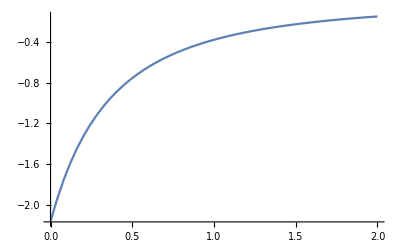

```mathematica
Plot[
trgegm⟦5,2⟧
,{Q2,0.,2.},PlotRange->Full]
```

## loopd0

```mathematica
octetname={"1Σm","2Σ0","3Σp","4pr","5ne" ,"6Ξm","7Ξ0","8Λ"};
```

loop derivative coefficient

to order 0

{loopged0,loopgmd0}

nugegm⟦consti,oct,F1F2⟧4*8*2

```mathematica
{loopged0,loopgmd0}=Transpose[(*[oct,loop,consti]8*2*13 transpose into [loop,consti,oct][2*13*8]*)
Table[
{
nugegm⟦;;,oct,1⟧,
(*++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
nugegm⟦;;,oct,2⟧
}
,{oct,1,8,1}
]
,{3,1,2}];//AbsoluteTiming
(*{loopged0,loopgmd0} ⟦seva,oct⟧[13,8]*)
```

{0.0032992,Null}

```mathematica
loopged0//Dimensions
loopgmd0//Dimensions
```

{13,8}

{13,8}

## rencon calc

constants

octetmagetonc1={(*1*)-c1/3,(*2*)c1/3,(*3*)c1,(*4*)c1,(*5*)-(2 c1)/3,(*6*)-c1/3,(*7*)-(2 c1)/3,(*8*)-c1/3};

```mathematica
Once[
octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
}
];
```

```mathematica
Once[
octetmageton={(*1*) −1.160,(*2*) 0.60,(*3*)2.458,
  (*4*)2.7928473446, (*5*)−1.9130427,
  (*6*)−0.6507,(*7*)−1.250,
 (*8*)−0.613}
 ];
```

rencon1

```mathematica
(*trgegm is [consti,io, gegem][4*8*2]*)
(*loopged0,loopgmd0 is ⟦seva,io⟧[13,8]*)
```

```mathematica
rencon=Table[1,{seva,1,13,1},{io,1,8,1}];
(*+++++++++++++++++renormalized according to charge+++++++++++++*)
Table[
rencon⟦;;,io⟧=
Re[octetcharge⟦io⟧/(
(trf1f2⟦1,io,1⟧/.Q2->0)+
(Cancel[Chop[loopged0⟦1,io⟧,choplimit]]/.{Q2->0})
)]
,{io,{1,3,4,6}}
];
(*+++++++++++++++renormalized isospin+++++++++++++++++++++*)
rencon⟦;;,2⟧=rencon⟦;;,3⟧;
rencon⟦;;,5⟧=rencon⟦;;,4⟧;
rencon⟦;;,7⟧=rencon⟦;;,6⟧;
rencon⟦;;,8⟧=Re[1/(1+(
Cancel[Chop[loopged0⟦2,8⟧,choplimit]]/.{Q2->0}
))];
(*++++++++++++++++++++no renormalized+++++++++++++++++++++*)
(*rencon⟦2,1⟧=1;
rencon⟦2,6⟧=1;
rencon⟦3,3⟧=1;
rencon⟦3,7⟧=1;
rencon⟦4,4⟧=1;
rencon⟦4,5⟧=1;*)
(*++++++++++++++++++++display+++++++++++++++++++++*)
TableForm[rencon,TableHeadings->{Automatic,None}]
```

1 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
2 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
3 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
4 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
5 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
6 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
7 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
8 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
9 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
10 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
11 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
12 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188
13 | 0.59289 | 0.59289 | 0.59289 | 0.564413 | 0.564413 | 0.658798 | 0.658798 | 0.610188

## Q2 table

Q2  table initial

```mathematica
(*trf1f2 is [consti,octet,treef1f2][4*8*2]*)
(*trgegm is [consti,octet,treegegem][4*8*2]*)
```

```mathematica
Once[octetcharge={
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
}];
```

```mathematica
Once[octetmageton={
(*1*)−1.160,(*2*)0.60,(*3*)2.458,
(*4*)2.7928473446,(*5*)−1.9130427,
(*6*)−0.6507,(*7*)−1.250,
(*8*)−0.613
}];
```

```mathematica
Once[octet`ge`gm={
{
(*1*)-1,(*2*)0,(*3*)1,
(*4*)1,(*5*)0,
(*6*)-1,(*7*)0,
(*8*)0
},
{
(*1*)−1.160,(*2*)0.60,(*3*)2.458,
(*4*)2.7928473446,(*5*)−1.9130427,
(*6*)−0.6507,(*7*)−1.250,
(*8*)−0.613
}
}];
```

```mathematica
getree=Re[trgegm⟦;;,;;,1⟧/.Q2->0];
```

```mathematica
gmtree=Re[trgegm⟦;;,;;,2⟧/.Q2->0];
```

```mathematica
gegmtree=Re[trgegm/.Q2->0];
```

```mathematica
tab`octetnameabbr=
{"term","Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"};
```

```mathematica
term`name={{"tree","loop","tot","exp.","diff"},
{"tree","loop","tot","exp.","diff","per"}
};
```

```mathematica
(*getree is [consti,octet,][4*8]*)
(*gmtree is [consti,octet,][4*8]*)
(*gegmtree is [consti,octet,treegegem][4*8*2]*)
```

```mathematica
geconstiname={"Ge.all","Ge.u","Ge.d","Ge.s"};
gmconstiname={"Gm.all","Gm.u","Gm.d","Gm.s"};
```

ge & gm

```mathematica
Dimensions/@{nugegm,loopged0,loopgmd0}
```

```mathematica
(*nugegm is [consti,octet,treegegem][13*8*2]equal loopged0 loopgdm0*)
(*{cur2ereci,cur2mreci} are ⟦consti,oct⟧[4,8]*)
```

fucoeandmrrlraw: 4 tot,u,d,s
Transpose[chpt`qfb`quench`coemass,{2,3,1}]:5u,6d,7s
Transpose[chpt`qfa`valence`coemass,{2,3,1}]:8u,9d,10s
Transpose[chpt`qfa`sea`coemass,{2,3,1}]:11u,12d,13s

## fun`Q2table`format

```mathematica
fun`Q2table`format=Function[{legendname,columnname,rowname,datalist},
Labeled[
Grid[(*grid start*)
(Prepend[(*add names row*)
MapThread[Prepend,{(*add names column*)
datalist,(*add the data to display*)
columnname(*prepend names column *)
}
]
,rowname(* prepend names  row *)
])(*⟦;;,{1,5,6}⟧*)
(*++++++++++only adopt the  proton neutron++++++++++++++++*)
,Frame->{All,All}
,Spacings->{2,2}
,Background->{None,{{None,None}}}
](*grid end*)
,legendname
,{{Top,Left}}
,LabelStyle->Directive[Red,Bold,20,FontFamily->"Times New Roman"]
]
];
```

## fun`Q2table`format apply.ed3

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
tab`zero`value`seavalence=Style[
Column[(*add divider lines*)
Table[
tetable=Chop[
Re[Cancel[Chop[({loopged0,loopgmd0}⟦gegmord⟧),choplimit]]/.Q2->0]
(*gives loop zero term, choose loopged0 or loopgmd0*)

,choplimit];
Multicolumn[
{(* paras of column need an {} *)
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
fun`Q2table`format[
{"Ge.loop.quench-sea-valence","Gm.loop.quench-sea-valence"}⟦gegmord⟧,(*legend name*)
{
"u-quench","d-quench","s-quench",
"u-di-valence","d-di-valence","s-di-valence",
"u-tot-valence","d-tot-valence","s-tot-valence",
"u-sea","d-sea","s-sea",
"u-loop.tot","d-loop.tot","s-loop.tot"
},(*column name*)
tab`octetnameabbr,(*row name*)
(*****************************data list start********************************)
{
(*down u d s quench 5 6 7 *)
rencon⟦2⟧*tetable⟦5⟧,
rencon⟦3⟧*tetable⟦6⟧,
rencon⟦4⟧*tetable⟦7⟧,
(*down u d s disconnected insert valence in sea 8 9 10 *)
rencon⟦2⟧*tetable⟦8⟧,
rencon⟦3⟧*tetable⟦9⟧,
rencon⟦4⟧*tetable⟦10⟧,
(*down u d s quench+di-valence in sea 8 9 10 *)
rencon⟦2⟧*(tetable⟦5⟧+tetable⟦8⟧),
rencon⟦3⟧*(tetable⟦6⟧+tetable⟦9⟧),
rencon⟦4⟧*(tetable⟦7⟧+tetable⟦10⟧),
(*down u d s sea 11 12 13 *)
rencon⟦2⟧*tetable⟦11⟧,
rencon⟦3⟧*tetable⟦12⟧,
rencon⟦4⟧*tetable⟦13⟧,
(*down quench-sea-valence summation for flavor *)
rencon⟦2⟧*Total[tetable⟦{5,8,11}⟧,{1}],(*u total 5 8 11*)
rencon⟦3⟧*Total[tetable⟦{6,9,12}⟧,{1}],(*d total 6 9 12*)
rencon⟦4⟧*Total[tetable⟦{7,10,13}⟧,{1}](*s total 7 10 13*)
(*up quench-sea-valence summation for flavor *)
}
(********************************data list end*******************************************)
]
(*+++++++++++++++++++++++++sea-valence part  +++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++*)
}
,1
],
{gegmord,1,2,1}
(*table index gegmord ge1, gm2*)
]
,Left(*alignment*)
,Spacings->4
]
,FontSize->8
]
```

term | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
u-quench | 0. | -0.085889 | 0.190201 | 0.347733 | 0.173867 | 0. | 0.0909315 | 0.105206
d-quench | 0.190201 | -0.085889 | 0. | 0.173867 | 0.347733 | 0.0909315 | 0. | 0.105206
s-quench | 0.0951007 | -0.085889 | 0.0951007 | 0. | 0. | 0.181863 | 0.181863 | 0.105206
u-di-valence | 0. | 0.500709 | 0.624019 | 0.52344 | 0.26172 | 0. | 0.250271 | 0.287037
d-di-valence | 0.624019 | 0.500709 | 0. | 0.26172 | 0.52344 | 0.250271 | 0. | 0.287037
s-di-valence | 0.31201 | 0.500709 | 0.31201 | 0. | 0. | 0.500542 | 0.500542 | 0.287037
u-tot-valence | 0. | 0.41482 | 0.814221 | 0.871173 | 0.435587 | 0. | 0.341202 | 0.392243
d-tot-valence | 0.814221 | 0.41482 | 0. | 0.435587 | 0.871173 | 0.341202 | 0. | 0.392243
s-tot-valence | 0.40711 | 0.41482 | 0.40711 | 0. | 0. | 0.682405 | 0.682405 | 0.392243
u-sea | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
d-sea | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
s-sea | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
u-loop.tot | 0. | 0.41482 | 0.814221 | 0.871173 | 0.435587 | 0. | 0.341202 | 0.392243
d-loop.tot | 0.814221 | 0.41482 | 0. | 0.435587 | 0.871173 | 0.341202 | 0. | 0.392243
s-loop.tot | 0.40711 | 0.41482 | 0.40711 | 0. | 0. | 0.682405 | 0.682405 | 0.392243Ge.loop.quench-sea-valence
term | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
u-quench | 0. | 0.0410688 | 0.525213 | 0.860039 | -0.512104 | 0. | -0.234652 | -0.0795471
d-quench | 0.525213 | 0.0410688 | 0. | -0.512104 | 0.860039 | -0.234652 | 0. | -0.0795471
s-quench | -0.203156 | -0.353415 | -0.203156 | 0. | 0. | 0.426905 | 0.426905 | 0.406216
u-di-valence | 0. | 0.437993 | 1.13769 | 0.847938 | -0.32521 | 0. | -0.362122 | -0.0351839
d-di-valence | 1.13769 | 0.437993 | 0. | -0.32521 | 0.847938 | -0.362122 | 0. | -0.0351839
s-di-valence | -0.231153 | -0.283607 | -0.231153 | 0. | 0. | 0.730899 | 0.730899 | 0.509831
u-tot-valence | 0. | 0.479062 | 1.66291 | 1.70798 | -0.837314 | 0. | -0.596774 | -0.114731
d-tot-valence | 1.66291 | 0.479062 | 0. | -0.837314 | 1.70798 | -0.596774 | 0. | -0.114731
s-tot-valence | -0.434309 | -0.637022 | -0.434309 | 0. | 0. | 1.1578 | 1.1578 | 0.916048
u-sea | -0.348164 | 0.142325 | -0.110874 | 0.0189382 | -0.112978 | 0.066321 | -0.00736348 | 0.0109451
d-sea | -0.110874 | 0.142325 | -0.348164 | -0.112978 | 0.0189382 | -0.00736348 | 0.066321 | 0.0109451
s-sea | -0.0147105 | 0.179634 | -0.0147105 | 0.00781139 | 0.00781139 | 0.00774773 | 0.00774773 | 0.00511932
u-loop.tot | -0.348164 | 0.621386 | 1.55203 | 1.72691 | -0.950292 | 0.066321 | -0.604137 | -0.103786
d-loop.tot | 1.55203 | 0.621386 | -0.348164 | -0.950292 | 1.72691 | -0.604137 | 0.066321 | -0.103786
s-loop.tot | -0.449019 | -0.457388 | -0.449019 | 0.00781139 | 0.00781139 | 1.16555 | 1.16555 | 0.921167Gm.loop.quench-sea-valence

```mathematica
Export[
FileNameJoin[{NotebookDirectory[],"/expression-results/","zero.value.sea-valence.L-1.00.pdf"}],
tab`zero`value`seavalence
]
```

C:\Users\Tom\Desktop\octet.sea-valence\expression-results\zero.value.sea-valence.L-1.00.pdf

consistency test

```mathematica
octetmageton`c1c2c3={
(*1 Σ*)-1+1/3 (c1-3 c2),c1/3,1+1/3 (c1+3 c2),
(*4 N*)1+1/3 (c1+3 c2),-(2 c1)/3,
(*6 Ξ*)-1+1/3 (c1-3 c2),-(2 c1)/3,
(*4 Λ*)-c1/3
};(*described by μu && μs (substitute with c1 c2 c3)*)
rencon⟦1⟧*gmtree⟦1⟧
rencon⟦1⟧*octetmageton`c1c2c3/.baselist2
```

{-0.579574,0.308618,1.19681,1.13933,-0.58759,-0.644002,-0.68585,-0.317622}

{-0.579574,0.308618,1.19681,1.13933,-0.58759,-0.644002,-0.68585,-0.317622}

## Q2 table respective

respective f1f2

```mathematica
renuff1=Table[0,{k,1,4,1}];
renuff2=Table[0,{k,1,4,1}];
Monitor[
Table[
(renuff1⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff1⟦diag⟧
)//.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{3}]);
(renuff2⟦constituent⟧=Total[
Table[
Simplify[
(
(
fucoe⟦constituent,diag,oct,coe⟧*ff2⟦diag⟧
)//.baselist⟦oct⟧
)/.fumass⟦constituent,diag,oct,coe⟧
]
,{oct,1,8,1}(*the outest level is the octet order*)
,{diag,1,11,1}(*the diag contris should be summed*)
,{coe,1,Length[fucoe⟦constituent,diag,oct⟧],1}(*the coe contris should be summed*)
]
,{3}]);
,{constituent,1,4,1}
];
,{constituent,oct,diag,coe}
]//AbsoluteTiming
(*combine ge gm from f1 f2 *)
(* nuff1,nuff2 is 4*8*11 *)
renugegm=Transpose[(* 8*2*4*11 transpose into 4*11*8*2 *)
Table[
-1/(16 π^2)*{
renuff1⟦;;,i,;;⟧-Q2/(4 constmo⟦i⟧^2)renuff2⟦;;,i,;;⟧,
renuff1⟦;;,i,;;⟧+renuff2⟦;;,i,;;⟧
}
,{i,1,8,1}]
,{3,4,1,2}
];//AbsoluteTiming
```

{17.1432,Null}

{0.0051414,Null}

```mathematica
renugegm//Dimensions
```

{4,11,8,2}

Q2  table.ed2

```mathematica
diagname2={"tree","1a","2b","3c","4de","5fg","6h","7i","8j","9kl","10mn","11op","tot.","diff","diff"};
constiname={"1all","2u","3d","4s"};
```

```mathematica
reconpersdiag=(Nest[Append[#,rencon]&,{rencon},10]);
reconpersdiag//Dimensions
```

{11,8}

## ge

```mathematica
(* renugegm [consti,diagram,oct,f1f2]{4,11,8,2} *)
```

```mathematica
Column[
Table[
Labeled[
tetable=Table[
Re[Simplify[Chop[renugegm⟦constiord,i,j,1⟧,choplimit]]/.Q2->0]
,{i,1,11,1}
,{j,1,8,1}
];
(*give the sign*)
tetablemod=tetable;
(*formatting, add other things *)
TableForm[
(*  add "tot.","gmexpect","diff" *)
Join[
{rencon⟦1⟧*(getree⟦constiord⟧)},
tetablemod,
{
rencon⟦1⟧*(getree⟦constiord⟧+Total[tetablemod,{1}]),
Round[rencon⟦1⟧*(getree⟦constiord⟧+Total[tetablemod,{1}])]-rencon⟦1⟧*(getree⟦constiord⟧+Total[tetablemod,{1}])
}
]
(*formatting*)
,TableHeadings->{
diagname2,
octetnameabbr
}
]
,Style[constiname⟦constiord⟧,"Section"],{{Top,Left}}
]
,{constiord,1,4,1}
]
,Spacings->1.5
]
```

| Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.714292 | 0. | 0.714292 | 0.680134 | 0. | -0.786641 | 0. | 0.
1a | -0.0638834 | 0.00267854 | 0.0692405 | 0.0694516 | -0.0672511 | -0.0168004 | -0.0185803 | -0.0130277
2b | -0.137189 | -0.019921 | 0.0973468 | 0.119781 | 0.230465 | -0.131784 | 0.0889532 | 0.0587293
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.0561723 | 0.00545548 | 0.0670832 | 0.0625687 | -0.0587327 | -0.0265593 | -0.0356485 | -0.0212974
6h | -0.00421838 | -0.0035484 | -0.00287843 | -0.00477466 | 0.00532704 | -0.00523835 | 0.00447232 | 0.000707294
7i | -0.0618989 | 0.0220602 | 0.106019 | 0.126303 | -0.0343797 | -0.0445966 | -0.0243334 | -0.00629402
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | -0.0120411 | -0.011266 | -0.0104908 | -0.017217 | 0.0210087 | -0.0129589 | 0.0131542 | 0.00397306
11op | -0.00711918 | -0.00724588 | -0.00737257 | -0.0067802 | 0.00804396 | -0.00797391 | 0.00670691 | 0.00161367
tot. | -1. | -2.83146×10^-14 | 1. | 1. | 1.1605×10^-13 | -1. | -7.91083×10^-13 | 1.13517×10^-13
diff | -1.11022×10^-16 | 2.83146×10^-14 | 0. | 0. | -1.1605×10^-13 | 0. | 7.91083×10^-13 | -1.13517×10^-131all
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 0. | 0.714292 | 1.42858 | 1.36027 | 0.680134 | 0. | 0.786641 | 0.737229
1a | -0.0638834 | 0.00267854 | 0.0692405 | 0.0694516 | -0.0672511 | -0.0168004 | -0.0185803 | -0.0130277
2b | 0.177522 | 0.294789 | 0.412057 | 0.492547 | 0.603232 | 0.0686763 | 0.289413 | 0.326265
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.0561723 | 0.00545548 | 0.0670832 | 0.0625687 | -0.0587327 | -0.0265593 | -0.0356485 | -0.0212974
6h | -0.00421838 | -0.0035484 | -0.00287843 | -0.00477466 | 0.00532704 | -0.00523835 | 0.00447232 | 0.000707294
7i | 0.0233787 | 0.107338 | 0.191297 | 0.223834 | 0.0631516 | 0.0261712 | 0.0464344 | 0.0826013
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | -0.0120411 | -0.011266 | -0.0104908 | -0.017217 | 0.0210087 | -0.0129589 | 0.0131542 | 0.00397306
11op | -0.00711918 | -0.00724588 | -0.00737257 | -0.0067802 | 0.00804396 | -0.00797391 | 0.00670691 | 0.00161367
tot. | 6.41704×10^-14 | 1. | 2. | 2. | 1. | -1.30227×10^-13 | 1. | 1.
diff | -6.41704×10^-14 | -9.25926×10^-14 | -1.20792×10^-13 | -3.81917×10^-14 | -1.53655×10^-13 | 1.30227×10^-13 | 9.21374×10^-13 | 1.11022×10^-162u
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 1.42858 | 0.714292 | 0. | 0.680134 | 1.36027 | 0.786641 | 0. | 0.737229
1a | 0.0692405 | 0.00267854 | -0.0638834 | -0.0672511 | 0.0694516 | -0.0185803 | -0.0168004 | -0.0130277
2b | 0.412057 | 0.294789 | 0.177522 | 0.603232 | 0.492547 | 0.289413 | 0.0686763 | 0.326265
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | 0.0810401 | 0.011787 | -0.057466 | -0.104481 | 0.120965 | -0.0347245 | -0.0253165 | -0.0244041
5fg | 0.0670832 | 0.00545548 | -0.0561723 | -0.0587327 | 0.0625687 | -0.0356485 | -0.0265593 | -0.0212974
6h | -0.00287843 | -0.0035484 | -0.00421838 | 0.00532704 | -0.00477466 | 0.00447232 | -0.00523835 | 0.000707294
7i | 0.191297 | 0.107338 | 0.0233787 | 0.0631516 | 0.223834 | 0.0464344 | 0.0261712 | 0.0826013
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | -0.0104908 | -0.011266 | -0.0120411 | 0.0210087 | -0.017217 | 0.0131542 | -0.0129589 | 0.00397306
11op | -0.00737257 | -0.00724588 | -0.00711918 | 0.00804396 | -0.0067802 | 0.00670691 | -0.00797391 | 0.00161367
tot. | 2. | 1. | 6.41704×10^-14 | 1. | 2. | 1. | -1.30227×10^-13 | 1.
diff | -7.54952×10^-15 | -9.25926×10^-14 | -6.41704×10^-14 | -1.53655×10^-13 | -3.81917×10^-14 | 9.21374×10^-13 | 1.30227×10^-13 | 1.11022×10^-163d
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 0.714292 | 0.714292 | 0.714292 | 0. | 0. | 1.57328 | 1.57328 | 0.737229
1a | -0.00535709 | -0.00535709 | -0.00535709 | -0.00220049 | -0.00220049 | 0.0353807 | 0.0353807 | 0.0260554
2b | 0.354553 | 0.354553 | 0.354553 | 0.0225202 | 0.0225202 | 0.24329 | 0.24329 | 0.150077
3c | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4de | -0.023574 | -0.023574 | -0.023574 | -0.0164837 | -0.0164837 | 0.060041 | 0.060041 | 0.0488083
5fg | -0.010911 | -0.010911 | -0.010911 | -0.00383594 | -0.00383594 | 0.0622078 | 0.0622078 | 0.0425949
6h | 0.00709681 | 0.00709681 | 0.00709681 | -0.000552378 | -0.000552378 | 0.000766021 | 0.000766021 | -0.00141459
7i | 0.0411571 | 0.0411571 | 0.0411571 | 0.00560785 | 0.00560785 | 0.139698 | 0.139698 | 0.101483
8j | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
9kl | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
10mn | 0.0225319 | 0.0225319 | 0.0225319 | -0.00379172 | -0.00379172 | -0.000195239 | -0.000195239 | -0.00794611
11op | 0.0144918 | 0.0144918 | 0.0144918 | -0.00126375 | -0.00126375 | 0.001267 | 0.001267 | -0.00322734
tot. | 1. | 1. | 1. | -7.82208×10^-14 | -7.82208×10^-14 | 2. | 2. | 1.
diff | -1.2057×10^-13 | -1.77192×10^-13 | -1.77192×10^-13 | 7.82208×10^-14 | 7.82208×10^-14 | -6.61249×10^-13 | -6.61249×10^-13 | 3.40616×10^-134s

## gm

```mathematica
Column[
Table[
Labeled[
tetable=Table[
Re[Simplify[Chop[renugegm⟦constiord,i,j,2⟧,choplimit]]/.Q2->0]
,{i,1,11,1}
,{j,1,8,1}
];
(*give the sign*)
tetablemod=tetable;
(*formatting, add other things *)
TableForm[
(*  add "tot.","gmexpect","diff" *)
Join[
{rencon⟦1⟧*(gmtree⟦constiord⟧)},
tetablemod,
{
rencon⟦1⟧*(gmtree⟦constiord⟧)+Total[tetablemod,{1}],
Round[rencon⟦1⟧*(gmtree⟦constiord⟧+Total[tetablemod,{1}])]-rencon⟦1⟧*(gmtree⟦constiord⟧+Total[tetablemod,{1}])
}
]
(*formatting*)
,TableHeadings->{
diagname2,
octetnameabbr
}
]
,Style[constiname⟦constiord⟧,"Section"],{{Top,Left}}
]
,{constiord,1,4,1}
]
,Spacings->1.5
]
```

| Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.49548 | 0.49548 | 1.48644 | 1.41536 | -0.943573 | -0.545667 | -1.09133 | -0.511391
1a | -0.367197 | 0.0200876 | 0.407372 | 0.398683 | -0.382041 | -0.0744865 | -0.0587635 | -0.0374738
2b | -0.00628454 | -0.00257824 | 0.00112806 | 0.00908518 | 0.0160236 | -0.00673283 | 0.00508738 | 0.00609903
3c | -0.0853004 | -0.00916843 | 0.0669635 | 0.0817439 | -0.0314628 | -0.0439357 | -0.0210462 | -0.0187096
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.257587 | 0.0370242 | 0.331636 | 0.304423 | -0.274784 | -0.100907 | -0.122183 | -0.0593334
6h | 0.0352964 | 0.0178258 | 0.000355271 | 0.0690866 | -0.0775355 | 0.0558069 | -0.062538 | -0.00978052
7i | -0.0013658 | 0.000548604 | 0.00246301 | -0.00192795 | 0.000701335 | -0.00173262 | -0.0014758 | 0.000231942
8j | -0.0882139 | 0.03351 | 0.155234 | 0.16938 | -0.0465872 | -0.0563002 | -0.0261195 | -0.00861953
9kl | -0.0776795 | 0.129947 | 0.337573 | 0.40521 | -0.395766 | -0.0538522 | -0.229222 | -0.159065
10mn | 0.00401372 | 0.00375532 | 0.00349692 | 0.005739 | -0.0070029 | 0.00431965 | -0.00438473 | -0.00132435
11op | 0.0494552 | 0.0359802 | 0.0225052 | 0.0777167 | -0.0955227 | 0.0679546 | -0.0829415 | -0.020544
tot. | -1.34781 | 0.774199 | 2.89621 | 3.05546 | -2.34203 | -0.780849 | -1.72965 | -0.844314
diff | 0.104292 | 0.305433 | -0.493426 | 0.469149 | -0.105287 | -0.269329 | -0.406544 | -0.2431691all
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 0. | 0.990961 | 1.98192 | 1.88715 | -0.471787 | 0. | -0.545667 | 2.00329×10^-16
1a | -0.367197 | 0.0200876 | 0.407372 | 0.398683 | -0.382041 | -0.0744865 | -0.0587635 | -0.0374738
2b | -0.00411223 | -0.000405928 | 0.00330037 | 0.0393651 | 0.0463034 | 0.00218367 | 0.0140039 | 0.0259816
3c | -0.0491543 | 0.0269776 | 0.10311 | 0.125442 | 0.0122356 | -0.0186891 | 0.00420035 | 0.0145959
4de | -0.057466 | 0.011787 | 0.0810401 | 0.120965 | -0.104481 | -0.0253165 | -0.0347245 | -0.0244041
5fg | -0.257587 | 0.0370242 | 0.331636 | 0.304423 | -0.274784 | -0.100907 | -0.122183 | -0.0593334
6h | 0.0352964 | 0.0178258 | 0.000355271 | 0.0690866 | -0.0775355 | 0.0558069 | -0.062538 | -0.00978052
7i | 0.00102862 | 0.00294302 | 0.00485742 | -0.00359326 | -0.000963974 | 0.00214407 | 0.00240088 | 0.0024326
8j | 0.0314227 | 0.153147 | 0.274871 | 0.300657 | 0.08469 | 0.0301829 | 0.0603636 | 0.100431
9kl | -0.0776795 | 0.129947 | 0.337573 | 0.40521 | -0.395766 | -0.0538522 | -0.229222 | -0.159065
10mn | 0.00401372 | 0.00375532 | 0.00349692 | 0.005739 | -0.0070029 | 0.00431965 | -0.00438473 | -0.00132435
11op | 0.0494552 | 0.0359802 | 0.0225052 | 0.0777167 | -0.0955227 | 0.0679546 | -0.0829415 | -0.020544
tot. | -0.691979 | 1.43003 | 3.55204 | 3.73084 | -1.66666 | -0.11066 | -1.05946 | -0.168484
diff | 0.494275 | -0.304584 | -0.103443 | -0.141106 | 0.284458 | 0.0870495 | -0.0501658 | 0.1242112u
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | 1.98192 | 0.990961 | 0. | -0.471787 | 1.88715 | -0.545667 | 0. | 2.00329×10^-16
1a | 0.407372 | 0.0200876 | -0.367197 | -0.382041 | 0.398683 | -0.0587635 | -0.0744865 | -0.0374738
2b | 0.00330037 | -0.000405928 | -0.00411223 | 0.0463034 | 0.0393651 | 0.0140039 | 0.00218367 | 0.0259816
3c | 0.10311 | 0.0269776 | -0.0491543 | 0.0122356 | 0.125442 | 0.00420035 | -0.0186891 | 0.0145959
4de | 0.0810401 | 0.011787 | -0.057466 | -0.104481 | 0.120965 | -0.0347245 | -0.0253165 | -0.0244041
5fg | 0.331636 | 0.0370242 | -0.257587 | -0.274784 | 0.304423 | -0.122183 | -0.100907 | -0.0593334
6h | 0.000355271 | 0.0178258 | 0.0352964 | -0.0775355 | 0.0690866 | -0.062538 | 0.0558069 | -0.00978052
7i | 0.00485742 | 0.00294302 | 0.00102862 | -0.000963974 | -0.00359326 | 0.00240088 | 0.00214407 | 0.0024326
8j | 0.274871 | 0.153147 | 0.0314227 | 0.08469 | 0.300657 | 0.0603636 | 0.0301829 | 0.100431
9kl | 0.337573 | 0.129947 | -0.0776795 | -0.395766 | 0.40521 | -0.229222 | -0.0538522 | -0.159065
10mn | 0.00349692 | 0.00375532 | 0.00401372 | -0.0070029 | 0.005739 | -0.00438473 | 0.00431965 | -0.00132435
11op | 0.0225052 | 0.0359802 | 0.0494552 | -0.0955227 | 0.0777167 | -0.0829415 | 0.0679546 | -0.020544
tot. | 3.55204 | 1.43003 | -0.691979 | -1.66666 | 3.73084 | -1.05946 | -0.11066 | -0.168484
diff | -0.103443 | -0.304584 | 0.494275 | 0.284458 | -0.141106 | -0.0501658 | 0.0870495 | 0.1242113d
 | Σm | Σ0 | Σp | pr | ne | Ξm | Ξ0 | Λ
tree | -0.49548 | -0.49548 | -0.49548 | 0. | 0. | 2.18267 | 2.18267 | 1.53417
1a | -0.0401752 | -0.0401752 | -0.0401752 | -0.0166416 | -0.0166416 | 0.13325 | 0.13325 | 0.0749475
2b | 0.00732879 | 0.00732879 | 0.00732879 | 0.00517112 | 0.00517112 | 0.010562 | 0.010562 | 0.00768455
3c | 0.0544829 | 0.0544829 | 0.0544829 | -0.00658261 | -0.00658261 | 0.0902285 | 0.0902285 | 0.0707246
4de | -0.023574 | -0.023574 | -0.023574 | -0.0164837 | -0.0164837 | 0.060041 | 0.060041 | 0.0488083
5fg | -0.0740484 | -0.0740484 | -0.0740484 | -0.0296386 | -0.0296386 | 0.22309 | 0.22309 | 0.118667
6h | -0.0356517 | -0.0356517 | -0.0356517 | 0.00844898 | 0.00844898 | 0.0067311 | 0.0067311 | 0.019561
7i | 0.00129721 | 0.00129721 | 0.00129721 | -0.000438696 | -0.000438696 | 0.00708509 | 0.00708509 | 0.00173678
8j | 0.0526166 | 0.0526166 | 0.0526166 | 0.00848436 | 0.00848436 | 0.168903 | 0.168903 | 0.126289
9kl | -0.259894 | -0.259894 | -0.259894 | -0.00944391 | -0.00944391 | 0.283074 | 0.283074 | 0.318129
10mn | -0.00751064 | -0.00751064 | -0.00751064 | 0.00126391 | 0.00126391 | 0.0000650797 | 0.0000650797 | 0.0026487
11op | -0.0719604 | -0.0719604 | -0.0719604 | 0.0178061 | 0.0178061 | 0.0149869 | 0.0149869 | 0.041088
tot. | -0.892569 | -0.892569 | -0.892569 | -0.0380547 | -0.0380547 | 3.18068 | 3.18068 | 2.36446
diff | -0.220882 | -0.220882 | -0.220882 | 0.0258823 | 0.0258823 | 0.0322516 | 0.0322516 | -0.1462834s